```mathematica
start1={1,1,1,{0,0},{0,-.9},{0,.9},{0,0},{1,0},{-2,0}*0.8}(** where they diverge at the end **)
```

{1,1,1,{0,0},{0,-0.9},{0,0.9},{0,0},{1,0},{-1.6,0.}}

```mathematica
start2={0.2,1.0,1.0,{0.7,-0.5},
{0.45624999999999805,-0.40000000000000036},
{0.48649999999999305,0.7108035714285776},{-2.0040641721428596,0.7343300157142867},{-1.7793716557142911,-0.7233028885714339},{-0.3207572564285184,-0.12968784142860894}}
(** where the spiral-like trajectory continues for a while **)
```

{0.2,1.,1.,{0.7,-0.5},{0.45625,-0.4},{0.4865,0.710804},{-2.00406,0.73433},{-1.77937,-0.723303},{-0.320757,-0.129688}}

```mathematica
data0=simulate[start2,50];
```

```mathematica
Manipulate[ParametricPlot[data0[All,"Position",t],{t,0.01,tmax}],{tmax,0.01,data0[[2]]}]
```

ParametricPlot::plld: Endpoints for t in {t,0.01,FE`tmax$$29} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
findPosition[list_,element_,tolerance_]:=
With[{},For[i=1,i≤ Length[list],i++,If[Norm[list[[i]]-element]<tolerance,Return[i]]];Return[-1]];(**With[{},Scan[If[Norm[#-element]<tolerance,Return[FirstPosition[list,#]]]&,list];Return[-1]]**)
```

```mathematica
findPosition[list_,element_]:=findPosition[list,element,10^-2];
```

```mathematica
createDividingPoints[largelist_,smalllist_]:=
createDividingPoints[largelist,smalllist,10^-2]
```

```mathematica
createDividingPoints[largelist_,smalllist_,tolerance_]:=
Intersection[largelist,smalllist,SameTest->(Norm[#1-#2]<tolerance&)]
```

```mathematica
createDividingIndices[largelist_,dividingpoints_,tolerance_]:=
findPosition[largelist,#,tolerance]&/@dividingpoints
```

```mathematica
createDividingIndices[largelist_,dividingpoints_]:=
createDividingIndices[largelist,dividingpoints,10^-2]
```

```mathematica
segmentByDividingIndices[largelist_,dividingindices_]:=
Prepend[     largelist[[     dividingindices[[#]]+1;;dividingindices[[#+1]]      ]]& /@  Drop[Range[Length[dividingindices]],-1] ,  largelist[[     1;;dividingindices[[1]]   ]]    ]
```

```mathematica
getScore[sim_,x_,y_]:=getScore[sim,x,y,0.01]
```

```mathematica
(** Assumes particle 2 is creating small loops and particle 3 is creating large loops enclosing those small loops. **)
getScore[sim_,x_,y_,timestep_]:=
Module[{position2,position3,velocity2,velocity3,velocity2y,velocity3y,stabilitytime,dividingpoints,dividingindices,velocity2ysegments,terms},
(**Echo["1"];**)
stabilitytime=Min[sim[[2]],SimulationStabilityTime[sim]] (**After this the solution becomes trivial**);
(**Echo["2"];**)
position2=Table[sim[2,"Position"][t],{t,0,stabilitytime,timestep}];
(**Echo["3"];**)
position3=Table[sim[3,"Position"][t],{t,0,stabilitytime,timestep}];
(**Echo["4"];**)
velocity2y=Table[sim[2,"Velocity"][t][[2]],{t,0,stabilitytime,timestep}];
(**Echo["5"];**)
dividingpoints=createDividingPoints[position2,position3];
(**Echo["6"];**)
(**Echo["length dividingpoints = " <> ToString[Length[dividingpoints]]];**)
dividingindices=Sort@createDividingIndices[position2,dividingpoints];
(**Echo["7"];**)
(**Echo["length dividingindices = " <> ToString[Length[dividingindices]]];**)
velocity2ysegments=segmentByDividingIndices[velocity2y,dividingindices];
(**Echo[terms=(Total[#-1]&/@PeakDetect/@velocity2ysegments)];**)
Echo[ListLinePlot/@segmentByDividingIndices[position2,dividingindices]];
Return[N[100*Abs[Length[terms]-x]+40*Abs[Total[terms]-x*y]+20*Variance[terms]]];
]
```

```mathematica
simulate[statevector_,T_]:=NBodySimulation[Association["PairwisePotential"->"InverseSquare"],{1->Association["Mass"->statevector[[1]],"Position"->statevector[[4]],"Velocity"->statevector[[7]]],2->Association["Mass"->statevector[[2]],"Position"->statevector[[5]],"Velocity"->statevector[[8]]],3->Association["Mass"->statevector[[3]],"Position"->statevector[[6]],"Velocity"->statevector[[9]]]},T];
```

```mathematica
multiply[x_,y_]:=multiply[x,y,1000];
```

```mathematica
multiply[x_,y_,maxiterations_]:=multiply[x,y,maxiterations,0.01];
```

```mathematica
multiply[x_,y_,maxiterations_,timestep_]:=multiply[x,y,maxiterations,timestep,.5];
```

```mathematica
multiply[x_,y_,maxiterations_,timestep_,stepsize_]:=multiply[x,y,maxiterations,timestep,stepsize,5000];
```

```mathematica
multiply[x_,y_,maxiterations_,timestep_,stepsize_,T_]:=
Module[{oldscore,newscore,oldstate,newstate,newsim,count=0},
oldstate={1,1,1,{0,0},{0,-.9},{0,.9},{0,0},{1,0},{-2,0}*0.8};
oldscore=getScore[simulate[oldstate,T],x,y];
Do[
Echo[count];
newstate=oldstate+Join[RandomReal[{-stepsize,stepsize},3],RandomReal[{stepsize,stepsize},{6,2}]];
newsim=simulate[newstate,T];
newscore=getScore[newsim,x,y];
Echo["newscore = "<> newscore];
If[0<newscore<oldscore,
oldstate=newstate;
oldscore=newscore;
Echo["updating score to " <> newscore <> " with " <> newstate];
];
count++;
,maxiterations];
]
```

```mathematica
multiply[x_,y_,maxiterations_,timestep_,stepsize_,T_]:=
Module[{oldscore,newscore,oldstate,newstate,newsim,count=0},
oldstate={1,1,1,{0,0},{0,-.9},{0,.9},{0,0},{1,0},{-2,0}*0.8};
oldscore=getScore[simulate[oldstate,T],x,y];
Do[
Echo[count];
newstate=oldstate+Join[RandomReal[{-stepsize,stepsize},3],RandomReal[{stepsize,stepsize},{6,2}]];
newsim=simulate[newstate,T];
newscore=getScore[newsim,x,y];
Echo["newscore = "<> newscore];
If[0<newscore<oldscore,
oldstate=newstate;
oldscore=newscore;
Echo["updating score to " <> newscore <> " with " <> newstate];
];
count++;
,maxiterations];
]
```

```mathematica
{1,1,1,{0,0},{0,-.9},{0,.9},{0,0},{1,0},{-2,0}*0.8};
```

```mathematica
multiplyGiven[x_,y_,T_,{m1_,m2_,m3_,pos1_,pos2_,pos3_,vel1_,vel2_,vel3_}]:=
multiplyGiven[x,y,1000,0.1,0.05,T,{m1,m2,m3,pos1,pos2,pos3,vel1,vel2,vel3}];
```

```mathematica
multiplyGiven[x_,y_,maxiterations_,timestep_,stepsize_,T_,startingstate_]:=
Module[{oldscore,newscore,oldstate,newstate,newsim,count=0},
oldstate=startingstate;
oldscore=getScore[simulate[startingstate,T]];
Do[
Echo[count];
newstate=oldstate+Join[RandomReal[{-stepsize,stepsize},3],RandomReal[{stepsize,stepsize},{6,2}]];
newsim=simulate[newstate,T];
newscore=getScore[newsim,x,y];
Echo["newscore = "<> newscore];
If[0<newscore<oldscore,
oldstate=newstate;
oldscore=newscore;
Echo["updating score to " <> newscore <> " with " <> newstate];
];
count++;
,maxiterations];
]
```

## Example:

0

1

2

3

4

5

6

length dividingpoints = 26

7

length dividingindices = 26

{-73,0,-638,0,-137,0,-638,0,-136,0,-637,0,0,-137,0,-637,0,-138,-638,0,-138,0,-637,0,-138,0}

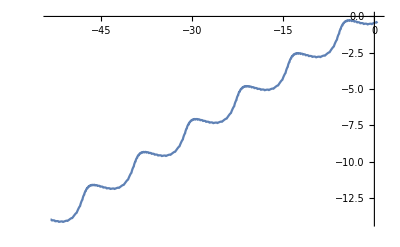

StringJoin::string: String expected at position 2 in newscore = <>20163740/13.

newscore = <>20163740/13

1

1

2

3

4

5

$Aborted

```mathematica
multiplyGiven[5,3,50,start2];
```

```mathematica
getScore[data0,3,5]
```

1

InterpolatingFunction::dmval: Input value {3000.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3000.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3000.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2

3

4

$Aborted

```mathematica
createDividingPoints[{{1,1},{1.5,1.6},{1.7,1.8}},{{1.7,1.8},{1.5,1.60333}}]
```

{{1.5,1.6},{1.7,1.8}}

```mathematica
createDividingIndices[{{1,1},{1.5,1.6},{1.7,1.8}},{{1.5,1.6},{1.7,1.8}}]
```

{2,3}

```mathematica
findPosition[{{1,1},{2,1}},{1.001,1},0.1]
```

1